```mathematica
(*Author: Oleg Kravchenko, 
Date: 11/09/15; 
Upd.01: 23/01/16*)
```

```mathematica
ClearAll["Global`*"]
```

### CIP - BS plots; Ref: NIFS-778, Basis Set Approach in the Constrained Interpolation Profile Method, T. Utsumi, J. Koga, T. Yabe, Y. Ogata, E. Matsunaga, T. Aoki and M. Sekine, July 2003

```mathematica
Parameters;
ImgSz=150;
```

Basic Functions;

```mathematica
BasisCIPBS[x_,k_,K_]:=Module[{ϕList,ϕL,ϕR,ϕ},
ϕK[x,K]:=Sum[Subscript[a, i] x^i,{i,0,2K+1,1}];
EqnSysL[k,K]:={
Table[If[l==k,(D[ϕK[x,K],{x,l}]/.x->0)==1,(D[ϕK[x,K],{x,l}]/.x->0)==0],{l,0,K,1}],
Table[(D[ϕK[x,K],{x,l}]/.x->-h)==0,{l,0,K,1}]
}//Flatten;
EqnSysR[k,K]:={
Table[If[l==k,(D[ϕK[x,K],{x,l}]/.x->0)==1,(D[ϕK[x,K],{x,l}]/.x->0)==0],{l,0,K,1}],
Table[(D[ϕK[x,K],{x,l}]/.x->h)==0,{l,0,K,1}]
}//Flatten;
ϕList={
ϕL=ϕK[x,K]/.Solve[EqnSysL[k,K],CoefficientList[ϕK[x,K],x]] ,
ϕR=ϕK[x,K]/.Solve[EqnSysR[k,K],CoefficientList[ϕK[x,K],x]],
(*ϕ=ϕL θ[x+1]+ϕR θ[x]*)
ϕ=Piecewise[{
{ϕL[[1]],-h≤x≤0},
{ϕR[[1]],0≤x≤h}
}]
}//Flatten
]
```

Auxillary;

```mathematica
D[ya[x],{x,2}]
```

Sin[4 π x]

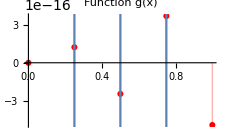
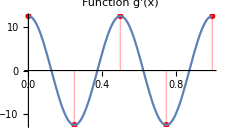
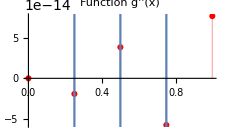
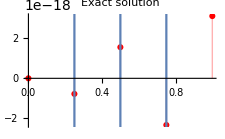
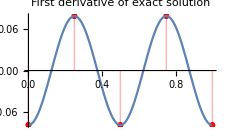
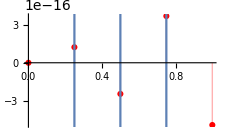

```mathematica
(*Function to be interpolated*)
g0[x_]:=Sin[4π x]
ya[x_]:=-1/(4π)^2 g0[x]
(*g0[x_]:=Cos[π x]
ya[x_]:=-g0[x]*)
d1ya[x_]:=D[ya[x],{x,1}]//Evaluate
d2ya[x_]:=D[ya[x],{x,2}]//Evaluate
g1[x_]:=D[g0[x],{x,1}]//Evaluate
g2[x_]:=D[g0[x],{x,2}]//Evaluate
g3[x_]:=D[g0[x],{x,3}]//Evaluate
(*Parameters*)
a=0;
b=1;
nx=5;
hx=(b-a)/(nx-1);
(*Arrays*)
xTbl=Table[a+k*hx,{k,0,nx-1,1}]//N;
g0Tbl=g0@xTbl;
g1Tbl=g1@xTbl;
g2Tbl=g2@xTbl;
g3Tbl=g3@xTbl;
yaTbl=ya@xTbl;
d1yaTbl=d1ya@xTbl;
d2yaTbl=d2ya@xTbl;
(*Indexes*)
Lc=1;;nx-2;
Cc=2;;nx-1;
Rc=3;;nx;

Row[{Show[{ListPlot[Partition[Riffle[xTbl,g0Tbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Function g(x)",PlotLegends->g0[x]],
Plot[g0[x],{x,a,b},ImageSize->1.ImgSz,PlotLabel->"Interpolant",PlotRange->All]}],Show[{ListPlot[Partition[Riffle[xTbl,g1Tbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Function g'(x)",PlotLegends->g1[x]],
Plot[g1[x],{x,a,b},ImageSize->1.ImgSz,PlotLabel->"Interpolant"]}],
Show[{ListPlot[Partition[Riffle[xTbl,g2Tbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Function g''(x)",PlotLegends->g2[x]],
Plot[g2[x],{x,a,b},ImageSize->1.ImgSz,PlotLabel->"Interpolant"]}],
Show[{ListPlot[Partition[Riffle[xTbl,yaTbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Exact solution",PlotLegends->ya[x]],
Plot[ya[x],{x,a,b},ImageSize->1.ImgSz,PlotLabel->"Interpolant"]}],
Show[{ListPlot[Partition[Riffle[xTbl,d1yaTbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"First derivative of exact solution",PlotLegends->d1ya[x]],
Plot[d1ya[x],{x,a,b},ImageSize->1.ImgSz,PlotLabel->"Interpolant"]}],
Show[{ListPlot[Partition[Riffle[xTbl,d2yaTbl],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Second derivative of exact solution",PlotLegends->d2ya[x]],
Plot[d2ya[x],{x,a,b},ImageSize->1.ImgSz,PlotLabel->"Interpolant"]}]

}]
```

#### CIP-BS^0;

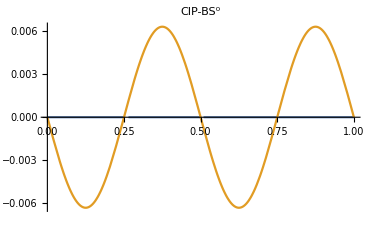
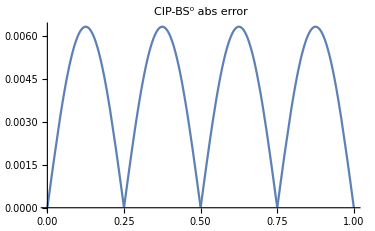
Numerical solution of Poisson equation f''(x) = TraditionalForm`sin(4\ π\ x)
Exact solution is y_a(x) = TraditionalForm`-sin(4\ π\ x)/16\ π^2
-Graphics--Graphics-

```mathematica
(*Matrix*)
ϕ0Matrix=-2/h IdentityMatrix[nx]+DiagonalMatrix[ConstantArray[1/h,nx-1],1]+DiagonalMatrix[ConstantArray[1/h,nx-1],-1];
(*Right hand side vector*)
gVector=0*g0Tbl;
gVector[[2;;nx-1]]=h/6 g0Tbl[[1;;nx-2]]+(2h)/3 g0Tbl[[2;;nx-1]]+h/6 g0Tbl[[3;;nx]];
(*BC*)
ϕ0Matrix[[1]][[1]]=1;ϕ0Matrix[[1]][[2]]=0;
ϕ0Matrix[[nx]][[nx]]=1;ϕ0Matrix[[nx]][[nx-1]]=0;
gVector[[1]]=ya[x]/.x->xTbl[[1]];
gVector[[nx]]=ya[x]/.x->xTbl[[nx]];
(*Disp*)
Row[{ϕ0Matrix//MatrixForm,Table[Subscript[f, i],{i,1,nx,1}]//MatrixForm,"=",gVector//MatrixForm}];
(*Solve the linear system*)
coeff=LinearSolve[ϕ0Matrix/.h->hx,gVector/.h->hx];
ϕ00=BasisCIPBS[x,0,0][[3]];
(*Reconstruct*)
ff=Sum[coeff[[k]]((ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify),{k,1,nx,1}]//Simplify;

(*Show Plots of the solution ans Error*)
imgTmp=Column[{" ",
"Numerical solution of Poisson equation f''(x) = "<>ToString[g0[x]//TraditionalForm],
"Exact solution is y_a(x) = "<>ToString[ya[x]//TraditionalForm],
Row[{Plot[{ff,ya[x]},{x,a,b},ImageSize->2.5ImgSz,PlotLabel->"CIP-BS^0"],
Plot[{Abs[ff-ya[x]]},{x,a,b},ImageSize->2.5ImgSz,PlotLabel->"CIP-BS^0 abs error"]}]
},Center]

(*Export["C:\\Users\\oleg-2\\Dropbox\\Collaboration\\nb\\img\\png\\poisson000_"<>ToString[nx]<>".png",imgTmp]*)
```

#### CIP-BS^1;

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6/(5 h) | -12/(5 h) | 6/(5 h) | 0 | 0 | 1/10 | 0 | -1/10 | 0 | 0
0 | 6/(5 h) | -12/(5 h) | 6/(5 h) | 0 | 0 | 1/10 | 0 | -1/10 | 0
0 | 0 | 6/(5 h) | -12/(5 h) | 6/(5 h) | 0 | 0 | 1/10 | 0 | -1/10
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1/10 | 0 | 1/10 | 0 | 0 | h/30 | -(4 h)/15 | h/30 | 0 | 0
0 | -1/10 | 0 | 1/10 | 0 | 0 | h/30 | -(4 h)/15 | h/30 | 0
0 | 0 | -1/10 | 0 | 1/10 | 0 | 0 | h/30 | -(4 h)/15 | h/30
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)(0.
0.+5.94828×10^-17 h
0.-1.18966×10^-16 h
0.+1.78449×10^-16 h
3.10207×10^-18
-0.0795775
0.-7.58115×10^-18 h^2-0.239359 h^3
7.58115×10^-18 h^2+0.239359 h^3
-7.58115×10^-18 h^2-0.239359 h^3
-0.0795775)

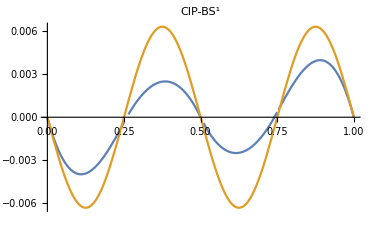
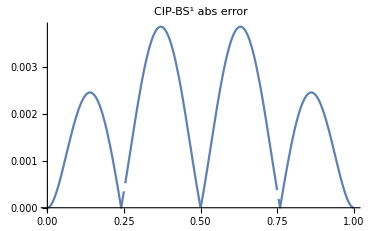
Numerical solution of Poisson equation f''(x) = TraditionalForm`sin(4\ π\ x)
Exact solution is y_a(x) = TraditionalForm`-sin(4\ π\ x)/16\ π^2
-Graphics--Graphics-

```mathematica
(*Matrix*)
ϕ11Matrix=-12/(5h)IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[6/(5h),nx-1],k],{k,-1,1,2}];
ϕ12Matrix=0IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[-1/10 k,nx-1],k],{k,-1,1,2}];
ϕ21Matrix=0IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[1/10 k,nx-1],k],{k,-1,1,2}];
ϕ22Matrix=-(4h)/15 IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[h/30,nx-1],k],{k,-1,1,2}];
(*BC*)
ϕ11Matrix[[1]][[1]]=1;ϕ11Matrix[[1]][[2]]=0;
ϕ11Matrix[[nx]][[nx]]=1;ϕ11Matrix[[nx]][[nx-1]]=0;
ϕ12Matrix[[1]][[1]]=0;ϕ12Matrix[[1]][[2]]=0;
ϕ12Matrix[[nx]][[nx]]=0;ϕ12Matrix[[nx]][[nx-1]]=0;
ϕ21Matrix[[1]][[1]]=0;ϕ21Matrix[[1]][[2]]=0;
ϕ21Matrix[[nx]][[nx]]=0;ϕ21Matrix[[nx]][[nx-1]]=0;
ϕ22Matrix[[1]][[1]]=1;ϕ22Matrix[[1]][[2]]=0;
ϕ22Matrix[[nx]][[nx]]=1;ϕ22Matrix[[nx]][[nx-1]]=0;
(*Right hand side vector*)
g1Vector=0*g0Tbl;
g2Vector=0*g0Tbl;
g1Vector[[Cc]]=(9 h)/70 g0Tbl[[Lc]]+(26 h)/35 g0Tbl[[Cc]]+(9 h)/70 g0Tbl[[Rc]]+(13 h^2)/420 g1Tbl[[Lc]]-(13 h^2)/420 g1Tbl[[Rc]];
g2Vector[[Cc]]=-(13 h^2)/420 g0Tbl[[Lc]]+(13 h^2)/420 g0Tbl[[Rc]]+h^3/140 g1Tbl[[Lc]]+(2 h^3)/105 g1Tbl[[Cc]]-h^3/140 g1Tbl[[Rc]];
(*BC*)
g1Vector[[1]]=yaTbl[[1]];
g1Vector[[nx]]=yaTbl[[nx]];
g2Vector[[1]]=d1yaTbl[[1]];
g2Vector[[nx]]=d1yaTbl[[nx]];
(*Joint Matrix & Right Hand Side Vector*)
ϕMatrix=Join[Join[ϕ11Matrix,ϕ12Matrix,2],Join[ϕ21Matrix,ϕ22Matrix,2]];
gVector=Join[g1Vector,g2Vector];

(*Disp*)
{ϕMatrix//MatrixForm,gVector//MatrixForm}//Row

(*Solve the linear system*)
coeff=LinearSolve[ϕMatrix/.h->hx,gVector/.h->hx];
ϕ00=BasisCIPBS[x,0,1][[3]];
ϕ01=BasisCIPBS[x,1,1][[3]];
(*Reconstruct*)
ff=Sum[coeff[[k]]((ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify)+coeff[[k+nx]]((ϕ01/.h->hx)/.x->x-xTbl[[k]]//Simplify),{k,1,nx,1}]//Simplify;

(*Show Plots of the solution ans Error*)
imgTmp=Column[{" ",
"Numerical solution of Poisson equation f''(x) = "<>ToString[g0[x]//TraditionalForm],
"Exact solution is y_a(x) = "<>ToString[ya[x]//TraditionalForm],
Row[{Plot[{ff,ya[x]},{x,a,b},ImageSize->2.5ImgSz,PlotLabel->"CIP-BS^1"],
Plot[{Abs[ff-ya[x]]},{x,a,b},ImageSize->2.5ImgSz,PlotLabel->"CIP-BS^1 abs error"]}]
},Center]
```

#### CIP-BS^2;

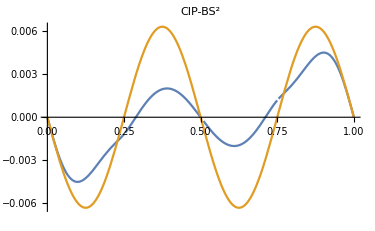
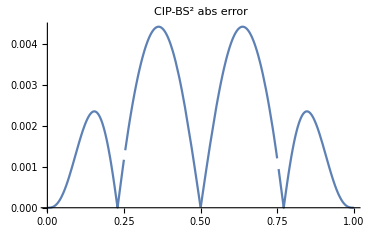
Numerical solution of Poisson equation f''(x) = TraditionalForm`sin(4\ π\ x)
Exact solution is y_a(x) = TraditionalForm`-sin(4\ π\ x)/16\ π^2
-Graphics--Graphics-

```mathematica
(*Matrix*)
ϕ11Matrix=-20/(7 h)IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[10/(7h),nx-1],k],{k,-1,1,2}];
ϕ12Matrix=0IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[-3/14 k,nx-1],k],{k,-1,1,2}];
ϕ13Matrix=-h/42 IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[h/84,nx-1],k],{k,-1,1,2}];
ϕ21Matrix=0IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[3/14 k,nx-1],k],{k,-1,1,2}];
ϕ22Matrix=-(16h)/35 IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[h/70,nx-1],k],{k,-1,1,2}];
ϕ23Matrix=0IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[-h^2/210 k,nx-1],k],{k,-1,1,2}];
ϕ31Matrix=-h/42 IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[h/84,nx-1],k],{k,-1,1,2}];
ϕ32Matrix=0IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[h^2/210 k,nx-1],k],{k,-1,1,2}];
ϕ33Matrix=-h^3/315 IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[-h^3/1260,nx-1],k],{k,-1,1,2}];
(*BC*)
ϕ11Matrix[[1]][[1]]=1;ϕ11Matrix[[1]][[2]]=0;
ϕ11Matrix[[nx]][[nx]]=1;ϕ11Matrix[[nx]][[nx-1]]=0;
ϕ12Matrix[[1]][[1]]=0;ϕ12Matrix[[1]][[2]]=0;
ϕ12Matrix[[nx]][[nx]]=0;ϕ12Matrix[[nx]][[nx-1]]=0;
ϕ13Matrix[[1]][[1]]=0;ϕ13Matrix[[1]][[2]]=0;
ϕ13Matrix[[nx]][[nx]]=0;ϕ13Matrix[[nx]][[nx-1]]=0;

ϕ21Matrix[[1]][[1]]=0;ϕ21Matrix[[1]][[2]]=0;
ϕ21Matrix[[nx]][[nx]]=0;ϕ21Matrix[[nx]][[nx-1]]=0;
ϕ22Matrix[[1]][[1]]=1;ϕ22Matrix[[1]][[2]]=0;
ϕ22Matrix[[nx]][[nx]]=1;ϕ22Matrix[[nx]][[nx-1]]=0;
ϕ23Matrix[[1]][[1]]=0;ϕ23Matrix[[1]][[2]]=0;
ϕ23Matrix[[nx]][[nx]]=0;ϕ23Matrix[[nx]][[nx-1]]=0;

ϕ31Matrix[[1]][[1]]=0;ϕ31Matrix[[1]][[2]]=0;
ϕ31Matrix[[nx]][[nx]]=0;ϕ31Matrix[[nx]][[nx-1]]=0;
ϕ32Matrix[[1]][[1]]=0;ϕ32Matrix[[1]][[2]]=0;
ϕ32Matrix[[nx]][[nx]]=0;ϕ32Matrix[[nx]][[nx-1]]=0;
ϕ33Matrix[[1]][[1]]=1;ϕ33Matrix[[1]][[2]]=0;
ϕ33Matrix[[nx]][[nx]]=1;ϕ33Matrix[[nx]][[nx-1]]=0;

(*Right hand side vector*)
g1Vector=0*g0Tbl;
g2Vector=0*g0Tbl;
g3Vector=0*g0Tbl;
g1Vector[[Cc]]=(25 h)/231 g0Tbl[[Lc]]+(181 h)/231 g0Tbl[[Cc]]+(25 h)/231 g0Tbl[[Rc]]+
(151 h^2)/4620 g1Tbl[[Lc]]-(151 h^2)/4620 g1Tbl[[Rc]]+
(181 h^3)/55440 g2Tbl[[Lc]]+(281 h^3)/27720 g2Tbl[[Cc]]+(181 h^3)/55440 g2Tbl[[Rc]];
g2Vector[[Cc]]=-(151 h^2)/4620 g0Tbl[[Lc]]+(151 h^2)/4620 g0Tbl[[Rc]]-
(19 h^3)/1980 g1Tbl[[Lc]]+(104 h^3)/3465-(19 h^3)/1980 g1Tbl[[Rc]]+
-(13 h^4)/13860 g2Tbl[[Lc]]+(13 h^4)/13860 g2Tbl[[Rc]];
g3Vector[[Cc]]=(181 h^3)/55440 g0Tbl[[Lc]]+(281 h^3)/27720 g0Tbl[[Cc]]+(181 h^3)/55440 g0Tbl[[Rc]]+
(13 h^4)/13860 g1Tbl[[Lc]]-(13 h^4)/13860 g1Tbl[[Rc]]+
h^5/11088 g2Tbl[[Lc]]+h^5/4620 g2Tbl[[Cc]]+h^5/11088 g2Tbl[[Rc]];
(*BC*)
g1Vector[[1]]=ya[x]/.x->xTbl[[1]];
g1Vector[[nx]]=ya[x]/.x->xTbl[[nx]];
g2Vector[[1]]=d1ya[x]/.x->xTbl[[1]];
g2Vector[[nx]]=d1ya[x]/.x->xTbl[[nx]];
g3Vector[[1]]=d2ya[x]/.x->xTbl[[1]];
g3Vector[[nx]]=d2ya[x]/.x->xTbl[[nx]];

(*Joint Matrix & Right Hand Side Vector*)
ϕMatrix=Join[Join[ϕ11Matrix,ϕ12Matrix,ϕ13Matrix,2],Join[ϕ21Matrix,ϕ22Matrix,ϕ23Matrix,2],Join[ϕ31Matrix,ϕ32Matrix,ϕ33Matrix,2]];
gVector=Join[g1Vector,g2Vector,g3Vector];

(*Disp*)
{ϕMatrix//MatrixForm,gVector//MatrixForm}//Row;

(*Solve the linear system*)
coeff=LinearSolve[ϕMatrix/.h->hx,gVector/.h->hx];
ϕ00=BasisCIPBS[x,0,2][[3]];
ϕ01=BasisCIPBS[x,1,2][[3]];
ϕ02=BasisCIPBS[x,2,2][[3]];
(*Reconstruct*)
ff=Sum[coeff[[k]]((ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify)+
coeff[[k+nx]]((ϕ01/.h->hx)/.x->x-xTbl[[k]]//Simplify)+
coeff[[k+2nx]]((ϕ02/.h->hx)/.x->x-xTbl[[k]]//Simplify),{k,1,nx,1}]//Simplify;

(*Show Plots of the solution ans Error*)
imgTmp=Column[{" ",
"Numerical solution of Poisson equation f''(x) = "<>ToString[g0[x]//TraditionalForm],
"Exact solution is y_a(x) = "<>ToString[ya[x]//TraditionalForm],
Row[{Plot[{ff,ya[x]},{x,a,b},ImageSize->2.5ImgSz,PlotLabel->"CIP-BS^2"],
Plot[{Abs[ff-ya[x]]},{x,a,b},ImageSize->2.5ImgSz,PlotLabel->"CIP-BS^2 abs error"]}]
},Center]
```

```mathematica
yaTbl
d1yaTbl
```

{0.,-7.75517×10^-19,1.55103×10^-18,-2.32655×10^-18,3.10207×10^-18}

{-0.0795775,0.0795775,-0.0795775,0.0795775,-0.0795775}

#### IDO;

```mathematica
(*Matrix*)
ϕ11Matrix=-4/h^2 IdentityMatrix[nx-2]+Sum[DiagonalMatrix[ConstantArray[2/h^2,nx-3],k],{k,-1,1,2}];
ϕ12Matrix=0IdentityMatrix[nx-2]+Sum[DiagonalMatrix[ConstantArray[-1/(2 h)k,nx-3],k],{k,-1,1,2}];
ϕ21Matrix=0IdentityMatrix[nx-2]+Sum[DiagonalMatrix[ConstantArray[15/(2 h^3)k,nx-3],k],{k,-1,1,2}];
ϕ22Matrix=-12/h^2 IdentityMatrix[nx-2]+Sum[DiagonalMatrix[ConstantArray[-3/(2 h^2),nx-3],k],{k,-1,1,2}];
(*BC*)
(*ϕ11Matrix[[1]][[1]]=1;ϕ11Matrix[[1]][[2]]=0;
ϕ11Matrix[[nx]][[nx]]=1;ϕ11Matrix[[nx]][[nx-1]]=0;
ϕ12Matrix[[1]][[1]]=0;ϕ12Matrix[[1]][[2]]=0;
ϕ12Matrix[[nx]][[nx]]=0;ϕ12Matrix[[nx]][[nx-1]]=0;
ϕ21Matrix[[1]][[1]]=0;ϕ21Matrix[[1]][[2]]=0;
ϕ21Matrix[[nx]][[nx]]=0;ϕ21Matrix[[nx]][[nx-1]]=0;
ϕ22Matrix[[1]][[1]]=1;ϕ22Matrix[[1]][[2]]=0;
ϕ22Matrix[[nx]][[nx]]=1;ϕ22Matrix[[nx]][[nx-1]]=0;*)

ϕMatrix=Join[Join[ϕ11Matrix,ϕ12Matrix,2],Join[ϕ21Matrix,ϕ22Matrix,2]];
gVector=Join[g0Tbl[[2;;nx-1]],g1Tbl[[2;;nx-1]]];
(*BC*)
gVector[[1]]=gVector[[1]]-2/hx^2 yaTbl[[1]]-1/(2hx)d1yaTbl[[1]];
gVector[[nx-2]]=gVector[[nx-2]]-2/hx^2 yaTbl[[nx]]+1/(2hx)d1yaTbl[[nx]];
(*BC*)
gVector[[nx-1]]=gVector[[nx-1]]+15/(2 hx^3)yaTbl[[1]]+3/(2 hx^2)d1yaTbl[[1]];
gVector[[2(nx-2)]]=gVector[[2(nx-2)]]-15/(2 hx^3)yaTbl[[nx]]+3/(2 hx^2)d1yaTbl[[nx]];

(*Disp*)
{ϕMatrix//MatrixForm,gVector//MatrixForm}//Row

(*Solve the linear system*)
coeff=LinearSolve[ϕMatrix/.h->hx,gVector/.h->hx];
coeff0=coeff[[1;;nx-2]];
coeff1=coeff[[nx-1;;]];
coeff0=PrependTo[coeff0,yaTbl[[1]]];
coeff0=AppendTo[coeff0,yaTbl[[nx]]];
coeff1=PrependTo[coeff1,d1yaTbl[[1]]];
coeff1=AppendTo[coeff1,d1yaTbl[[nx]]];
```

(-4/h^2 | 2/h^2 | 0 | 0 | -1/(2 h) | 0
2/h^2 | -4/h^2 | 2/h^2 | 1/(2 h) | 0 | -1/(2 h)
0 | 2/h^2 | -4/h^2 | 0 | 1/(2 h) | 0
0 | 15/(2 h^3) | 0 | -12/h^2 | -3/(2 h^2) | 0
-15/(2 h^3) | 0 | 15/(2 h^3) | -3/(2 h^2) | -12/h^2 | -3/(2 h^2)
0 | -15/(2 h^3) | 0 | 0 | -3/(2 h^2) | -12/h^2)(0.159155
-2.44929×10^-16
-0.159155
-14.4762
12.5664
-14.4762)

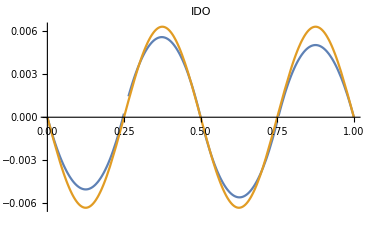
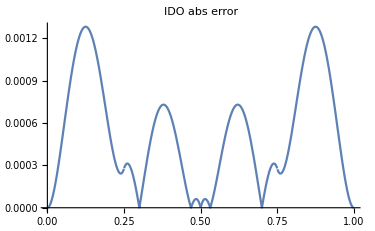
Numerical solution of Poisson equation f''(x) = TraditionalForm`sin(4\ π\ x)
Exact solution is y_a(x) = TraditionalForm`-sin(4\ π\ x)/16\ π^2
-Graphics--Graphics-

```mathematica
(*Reconstruct*)
ϕ00=BasisCIPBS[x,0,1][[3]];
ϕ01=BasisCIPBS[x,1,1][[3]];

(*ff=Sum[coeff0[[k]]((ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify)+coeff[[k+nx]]((ϕ01/.h->hx)/.x->x-xTbl[[k]]//Simplify),{k,1,nx,1}]//Simplify;*)
ff=Sum[coeff0[[k]]((ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify)+coeff1[[k]]((ϕ01/.h->hx)/.x->x-xTbl[[k]]//Simplify),{k,1,nx,1}]//Simplify;

(*Show Plots of the solution ans Error*)
imgTmp=Column[{" ",
"Numerical solution of Poisson equation f''(x) = "<>ToString[g0[x]//TraditionalForm],
"Exact solution is y_a(x) = "<>ToString[ya[x]//TraditionalForm],
Row[{Plot[{ff,ya[x]},{x,a-0hx,b+0hx},ImageSize->2.5ImgSz,PlotLabel->"IDO"],
Plot[{Abs[ff-ya[x]]},{x,a-0hx,b+0hx},ImageSize->2.5ImgSz,PlotLabel->"IDO abs error"]}]
},Center]
```

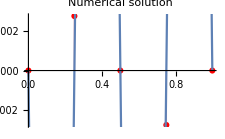

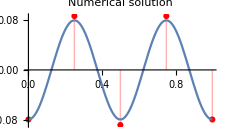

```mathematica
Show[{ListPlot[Partition[Riffle[xTbl,coeff0],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Numerical solution"],
Plot[ya[x],{x,a,b},ImageSize->1.ImgSz,PlotLabel->"Interpolant",PlotRange->Full]}]
Show[{ListPlot[Partition[Riffle[xTbl,coeff1],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Numerical solution"],
Plot[d1ya[x],{x,a,b},ImageSize->1.5ImgSz,PlotLabel->"Interpolant",PlotRange->Full]}]
```

#### IDOv2;

```mathematica
(*Matrix*)
ϕ11Matrix=-4/h^2 IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[2/h^2,nx-1],k],{k,-1,1,2}];
ϕ12Matrix=0IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[-1/(2 h)k,nx-1],k],{k,-1,1,2}];
ϕ21Matrix=0IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[15/(2 h^3)k,nx-1],k],{k,-1,1,2}];
ϕ22Matrix=-12/h^2 IdentityMatrix[nx]+Sum[DiagonalMatrix[ConstantArray[-3/(2 h^2),nx-1],k],{k,-1,1,2}];
(*BC*)
ϕ11Matrix[[1]][[1]]=1;ϕ11Matrix[[1]][[2]]=0;
ϕ11Matrix[[nx]][[nx]]=1;ϕ11Matrix[[nx]][[nx-1]]=0;
ϕ12Matrix[[1]][[1]]=0;ϕ12Matrix[[1]][[2]]=0;
ϕ12Matrix[[nx]][[nx]]=0;ϕ12Matrix[[nx]][[nx-1]]=0;
ϕ21Matrix[[1]][[1]]=0;ϕ21Matrix[[1]][[2]]=0;
ϕ21Matrix[[nx]][[nx]]=0;ϕ21Matrix[[nx]][[nx-1]]=0;
ϕ22Matrix[[1]][[1]]=1;ϕ22Matrix[[1]][[2]]=0;
ϕ22Matrix[[nx]][[nx]]=1;ϕ22Matrix[[nx]][[nx-1]]=0;

ϕMatrix=Join[Join[ϕ11Matrix,ϕ12Matrix,2],Join[ϕ21Matrix,ϕ22Matrix,2]];
gVector=Join[g0Tbl,g1Tbl];

(*Disp*)
{ϕMatrix//MatrixForm,gVector//MatrixForm}//Row

(*Solve the linear system*)
coeff=LinearSolve[ϕMatrix/.h->hx,gVector/.h->hx];
coeff0=coeff[[1;;nx]];
coeff1=coeff[[nx-1;;]];
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/h^2 | -4/h^2 | 2/h^2 | 0 | 0 | 1/(2 h) | 0 | -1/(2 h) | 0 | 0
0 | 2/h^2 | -4/h^2 | 2/h^2 | 0 | 0 | 1/(2 h) | 0 | -1/(2 h) | 0
0 | 0 | 2/h^2 | -4/h^2 | 2/h^2 | 0 | 0 | 1/(2 h) | 0 | -1/(2 h)
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-15/(2 h^3) | 0 | 15/(2 h^3) | 0 | 0 | -3/(2 h^2) | -12/h^2 | -3/(2 h^2) | 0 | 0
0 | -15/(2 h^3) | 0 | 15/(2 h^3) | 0 | 0 | -3/(2 h^2) | -12/h^2 | -3/(2 h^2) | 0
0 | 0 | -15/(2 h^3) | 0 | 15/(2 h^3) | 0 | 0 | -3/(2 h^2) | -12/h^2 | -3/(2 h^2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)(0.
1.22465×10^-16
-2.44929×10^-16
3.67394×10^-16
-4.89859×10^-16
12.5664
-12.5664
12.5664
-12.5664
12.5664)

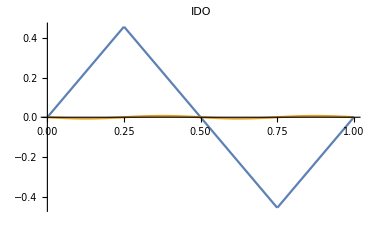
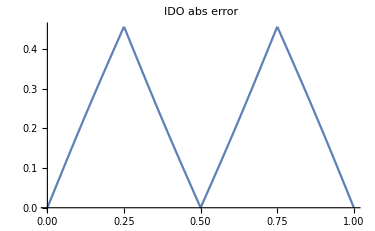
Numerical solution of Poisson equation f''(x) = TraditionalForm`sin(4\ π\ x)
Exact solution is y_a(x) = TraditionalForm`-sin(4\ π\ x)/16\ π^2
-Graphics--Graphics-

```mathematica
(*Reconstruct*)
ϕ00=BasisCIPBS[x,0,0][[3]];
ϕ01=BasisCIPBS[x,1,1][[3]];

(*ff=Sum[coeff0[[k]]((ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify)+coeff[[k+nx]]((ϕ01/.h->hx)/.x->x-xTbl[[k]]//Simplify),{k,1,nx,1}]//Simplify;*)
ff=Sum[coeff0[[k]]((ϕ00/.h->hx)/.x->x-xTbl[[k]]//Simplify),{k,1,nx,1}]//Simplify;

(*Show Plots of the solution ans Error*)
imgTmp=Column[{" ",
"Numerical solution of Poisson equation f''(x) = "<>ToString[g0[x]//TraditionalForm],
"Exact solution is y_a(x) = "<>ToString[ya[x]//TraditionalForm],
Row[{Plot[{ff,ya[x]},{x,a-0hx,b+0hx},ImageSize->2.5ImgSz,PlotLabel->"IDO"],
Plot[{Abs[ff-ya[x]]},{x,a-0hx,b+0hx},ImageSize->2.5ImgSz,PlotLabel->"IDO abs error"]}]
},Center]
```

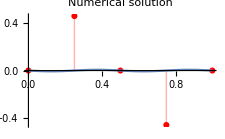

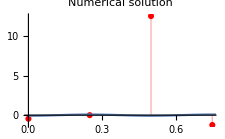

```mathematica
Show[{ListPlot[Partition[Riffle[xTbl,coeff0],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Numerical solution"],
Plot[ya[x],{x,a,b},ImageSize->1.ImgSz,PlotLabel->"Interpolant",PlotRange->Full]}]
Show[{ListPlot[Partition[Riffle[xTbl,coeff1],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Numerical solution"],
Plot[d1ya[x],{x,a,b},ImageSize->1.5ImgSz,PlotLabel->"Interpolant",PlotRange->Full]}]
```

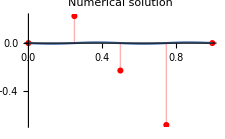

```mathematica
Show[{ListPlot[Partition[Riffle[xTbl,{0,coeff0[[2;;4]]-.23,0}//Flatten],2],PlotStyle->{Red},Filling->Axis,ImageSize->1.5ImgSz,PlotLabel->"Numerical solution"],
Plot[ya[x],{x,a,b},ImageSize->1.ImgSz,PlotLabel->"Interpolant",PlotRange->Full]}]
```